```mathematica
$Assumptions = {κ ∈ Reals, κ > 0,  x ∈ Reals, y ∈ Reals,j ∈ Integers,q ∈ Reals, θ ∈ Reals, v ∈ Reals, v >= 0, λ ∈ Reals, λ >0}
```

{κ∈ℝ,κ>0,x∈ℝ,y∈ℝ,j∈ℤ,q∈ℝ,θ∈ℝ,v∈ℝ,v≥0,λ∈ℝ,λ>0}

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

## mBZ

```mathematica
κ1x = κ Cos[0]
κ1y = κ Sin[0]
κ3x = κ Cos[2 π/3]
κ3y = κ Sin[2 π/3]
κ5x = κ Cos[4 π/3]
κ5y = κ Sin[4 π/3]
```

κ

0

-κ/2

(√3 κ)/2

-κ/2

-(√3 κ)/2

## RMG Berry Curvature (N_L=3)

```mathematica
ϕ = {1, λ (x + I y)}
χ = FullSimplify[Normalize[ϕ]]
Ωλ=  FullSimplify[ComplexExpand[-2 Im[Conjugate[D[χ, x]].D[χ, y]]]]
```

{1,(x+ⅈ y) λ}

{1/(√(1+(x^2+y^2) λ^2)),((x+ⅈ y) λ)/(√(1+(x^2+y^2) λ^2))}

-(2 λ^2)/((1+(x^2+y^2) λ^2)^2)

```mathematica
Ωconnecty = FullSimplify[ComplexExpand[Conjugate[χ].D[χ,y]]]
Ωconnectx = FullSimplify[ComplexExpand[Conjugate[χ].D[χ,x]]]
```

(ⅈ x λ^2)/(1+(x^2+y^2) λ^2)

-(ⅈ y λ^2)/(1+(x^2+y^2) λ^2)

```mathematica
connectx[x_, y_]:=-(ⅈ y λ^2)/(1+(x^2+y^2) λ^2)
connecty[x_, y_]:=(ⅈ x λ^2)/(1+(x^2+y^2) λ^2)
Ωλfunc[x_, y_] := -(2 λ^2)/((1+(x^2+y^2) λ^2)^2)
```

```mathematica
Ωλcontrib = FullSimplify[1/3(Ωλfunc[κ1x, κ1y] + Ωλfunc[κ3x, κ3y] + Ωλfunc[κ5x, κ5y])]
```

-(2 λ^2)/((1+κ^2 λ^2)^2)

```mathematica
Clear[x,y]
```

## Symmetric Potential

```mathematica
κ=1
```

1

```mathematica
Δ =FullSimplify[-1/(1 + λ^2 κ^2)*(1 + λ^2 κ ω)]
α = FullSimplify[ (I Sqrt[3] κ λ^2)/((1 + κ^2 λ^2)^2) * (1 - λ^2 κ^2 ω)]
```

-(1+(-1)^(2/3) λ^2)/(1+λ^2)

(√3 λ^2 (ⅈ+(-1)^(1/6) λ^2))/((1+λ^2)^2)

### Pure 3-patch

```mathematica
j = 1
nmz1 = FullSimplify[16 Re[ω^j Δ]^4 + 3 Abs[Δ]^4 + 8 Re[Δ^3] Re[ω^j Δ]]
Ω3p1 = FullSimplify[ComplexExpand[(2 Sqrt[3])/nmz1^2 * (8 v Re[ω^j Δ]^3 - 12 Re[Conjugate[Δ] α] Re[ω^j Δ]^2 + 3 Abs[Δ]^2 Re[Conjugate[Δ] α] + v Re[Δ^3]) (4 Re[ω^j Δ]^2 Im[Conjugate[Δ] α] + 4 Re[ω^j Δ] Im[α Δ^2] - v Im[Δ^3] + Abs[Δ]^2 Im[Conjugate[Δ] α]), {Δ, α}]]
```

1

(27 λ^4)/((1+λ^2)^4)

-(v (-1+λ^2) (6 λ^4+v (1+λ^2)^3))/(18 λ^4)

### Cross-Term

```mathematica
j=1
nmz0 = FullSimplify[16 Re[ω^j Δ]^4 + 3 Abs[Δ]^4 + 8 Re[Δ^3] Re[ω^j Δ]]
dxA1 = FullSimplify[-1/(2 Sqrt[nmz0]) (1/nmz0 (16 v Re[ω^j Δ]^3 - 24 Re[Conjugate[Δ] α] Re[ω^j Δ]^2 + 6 Abs[Δ]^2 Re[Conjugate[Δ] α] + 2 v Re[Δ^3]) (4 Re[ω^j Δ]^2 - Abs[Δ]^2) - 4 v Re[ω^j Δ] + 4 Re[Conjugate[Δ] α])]
dyA1 = 0
dxA3 = FullSimplify[-1/(2 Sqrt[nmz0]) (1/nmz0 (16 v Re[ω^j Δ]^3 - 24 Re[Conjugate[Δ] α] Re[ω^j Δ]^2 + 6 Abs[Δ]^2 Re[Conjugate[Δ] α] + 2 v Re[Δ^3]) (2 Conjugate[Δ] Re[ω^j Δ] + Δ^2) + 2 Conjugate[α] Re[ω^j Δ] - v Conjugate[Δ] - α Δ)]
dyA3 = FullSimplify[1/(2 Sqrt[nmz0]) (-2 Sqrt[3] Conjugate[α] Re[ω^j Δ] + Sqrt[3] Conjugate[Δ] v + Sqrt[3] Δ α)]
dxA5 = FullSimplify[-1/(2 Sqrt[nmz0]) (1/nmz0 (16 v Re[ω^j Δ]^3 - 24 Re[Conjugate[Δ] α] Re[ω^j Δ]^2 + 6 Abs[Δ]^2 Re[Conjugate[Δ] α] + 2 v Re[Δ^3]) (2 Δ Re[ω^j Δ] + Conjugate[Δ]^2) + 2 α Re[ω^j Δ] - Δ v - Conjugate[Δ] Conjugate[α])]
dyA5 = FullSimplify[1/(2 Sqrt[nmz0]) (2 Sqrt[3] α Re[ω^j Δ] - Sqrt[3] Δ v - Sqrt[3] Conjugate[Δ] Conjugate[α])]
```

1

(27 λ^4)/((1+λ^2)^4)

(6 λ^4+v (1+λ^2)^3)/(6 √3 λ^2 (1+λ^2))

0

(3 (-3 ⅈ+√3) λ^4+v (1+λ^2)^2 (-3 ⅈ-√3+2 √3 λ^2))/(36 (λ^2+λ^4))

(-3 (-3 ⅈ+√3) λ^4+v (1+λ^2)^2 (-2 √3+(3 ⅈ+√3) λ^2))/(12 √3 λ^2 (1+λ^2))

(3 (3 ⅈ+√3) λ^4+v (1+λ^2)^2 (3 ⅈ-√3+2 √3 λ^2))/(36 (λ^2+λ^4))

((3+3 ⅈ √3) λ^4+2 v (1+λ^2)^2 (1+(-1)^(2/3) λ^2))/(12 (λ^2+λ^4))

```mathematica
cross1 = FullSimplify[2 I/Sqrt[3] *( Re[1 * dxA1] * connecty[κ1x,κ1y]  - Re[1 * dyA1] *  connectx[κ1x,κ1y] +  Re[Conjugate[ω^1]* dxA3] *  connecty[κ3x,κ3y] - Re[Conjugate[ω^1] * dyA3] *  connectx[κ3x,κ3y] + Re[Conjugate[ω^2]* dxA5] *  connecty[κ5x,κ5y] - Re[Conjugate[ω^2] * dyA5] *  connectx[κ5x,κ5y])]
```

-(6 λ^4+v (1+λ^2)^3)/(3 (1+λ^2)^2)

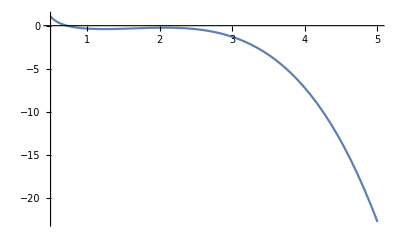

```mathematica
Plot[cross1 + Ωλcontrib + Ω3p1, {λ, 0.5, 5}]
```

## Anti-Symmetric Δ, α

```mathematica
Δ =FullSimplify[1/(1 + λ^2 κ^2)*(1 - λ^2 κ ω)]
α = FullSimplify[κ λ^2/((1 + κ^2 λ^2)^2) * (2 + I Sqrt[3] (1 - λ^2 κ^2 ω))]
```

3

(1-(-1)^(2/3) κ λ^2)/(1+κ^2 λ^2)

(κ λ^2 (2+ⅈ √3+(-1)^(1/6) √3 κ^2 λ^2))/((1+κ^2 λ^2)^2)

```mathematica
Clear[Δ, α]
```

## Cross Term (j = 1)

```mathematica
j = 1
nmz0 = FullSimplify[16 Re[ω^j Δ]^4 + 3 Abs[Δ]^4 + 8 Re[Δ^3] Re[ω^j Δ]]
dxA1 = FullSimplify[-1/(2 Sqrt[nmz0]) (1/nmz0 (16 v Re[ω^j Δ]^3 - 24 Re[Conjugate[Δ] α] Re[ω^j Δ]^2 + 6 Abs[Δ]^2 Re[Conjugate[Δ] α] + 2 v Re[Δ^3]) (4 Re[ω^j Δ]^2 - Abs[Δ]^2) - 4 v Re[ω^j Δ] + 4 Re[Conjugate[Δ] α])]
dyA1 = 0
dxA3 = FullSimplify[-1/(2 Sqrt[nmz0]) (1/nmz0 (16 v Re[ω^j Δ]^3 - 24 Re[Conjugate[Δ] α] Re[ω^j Δ]^2 + 6 Abs[Δ]^2 Re[Conjugate[Δ] α] + 2 v Re[Δ^3]) (2 Conjugate[Δ] Re[ω^j Δ] + Δ^2) + 2 Conjugate[α] Re[ω^j Δ] - v Conjugate[Δ] - α Δ)]
dyA3 = FullSimplify[1/(2 Sqrt[nmz0]) (-2 Sqrt[3] Conjugate[α] Re[ω^j Δ] + Sqrt[3] Conjugate[Δ] v + Sqrt[3] Δ α)]
dxA5 = FullSimplify[-1/(2 Sqrt[nmz0]) (1/nmz0 (16 v Re[ω^j Δ]^3 - 24 Re[Conjugate[Δ] α] Re[ω^j Δ]^2 + 6 Abs[Δ]^2 Re[Conjugate[Δ] α] + 2 v Re[Δ^3]) (2 Δ Re[ω^j Δ] + Conjugate[Δ]^2) + 2 α Re[ω^j Δ] - Δ v - Conjugate[Δ] Conjugate[α])]
dyA5 = FullSimplify[1/(2 Sqrt[nmz0]) (2 Sqrt[3] α Re[ω^j Δ] - Sqrt[3] Δ v - Sqrt[3] Conjugate[Δ] Conjugate[α])]
```

1

(27 λ^4)/((1+λ^2)^4)

(6 λ^4+v (1+λ^2)^3)/(6 √3 λ^2 (1+λ^2))

0

(3 (-3 ⅈ+√3) λ^4+v (1+λ^2)^2 (-3 ⅈ-√3+2 √3 λ^2))/(36 (λ^2+λ^4))

(-3 (-3 ⅈ+√3) λ^4+v (1+λ^2)^2 (-2 √3+(3 ⅈ+√3) λ^2))/(12 √3 λ^2 (1+λ^2))

(3 (3 ⅈ+√3) λ^4+v (1+λ^2)^2 (3 ⅈ-√3+2 √3 λ^2))/(36 (λ^2+λ^4))

((3+3 ⅈ √3) λ^4+2 v (1+λ^2)^2 (1+(-1)^(2/3) λ^2))/(12 (λ^2+λ^4))

```mathematica
v=0
```

0

```mathematica
Clear[x,y]
```

```mathematica
cross1 = FullSimplify[2 I *( Re[1 * dxA1] * connecty[κ1x,κ1y]  - Re[1 * dyA1] *  connectx[κ1x,κ1y] +  Re[Conjugate[ω^1]* dxA3] *  connecty[κ3x,κ3y] - Re[Conjugate[ω^1] * dyA3] *  connectx[κ3x,κ3y] + Re[Conjugate[ω^2]* dxA5] *  connecty[κ5x,κ5y] - Re[Conjugate[ω^2] * dyA5] *  connectx[κ5x,κ5y])]
```

(-6 λ^4-v (1+λ^2)^3)/(√3 (1+λ^2)^2)

```mathematica
x = 0
y = 0
Ωcross = FullSimplify[Series[2 I *( Re[1 * dxA1] * connecty[κ1x,κ1y]  - Re[1 * dyA1] *  connectx[κ1x,κ1y] +  Re[Conjugate[ω^1]* dxA3] *  connecty[κ3x,κ3y] - Re[Conjugate[ω^1] * dyA3] *  connectx[κ3x,κ3y] + Re[Conjugate[ω^2]* dxA5] *  connecty[κ5x,κ5y] - Re[Conjugate[ω^2] * dyA5] *  connectx[κ5x,κ5y]),{λ, 1, 4}]]
```

0

0

-(3+4 v)/(2 √3)-((3+2 v) (λ-1))/(√3)-(v (λ-1)^2)/(√3)+1/2 √3 (λ-1)^3-3/8 √3 (λ-1)^4+O[λ-1]^5

```mathematica
Clear[x,y]
```